```mathematica
ψ[r_]=({{1+(r1-r)/(r2-r1), (r-r1)/(r2-r1)}});
Integrate[Transpose[ψ[r]].ψ[r],{r,r1,r2}]//MatrixForm
Integrate[Transpose[D[ψ[r],r]].D[ψ[r],r],{r,r1,r2}]//MatrixForm
```

(-r1/3+r2/3 | 1/6 (-r1+r2)
1/6 (-r1+r2) | -r1/3+r2/3)

(1/(-r1+r2) | -1/(-r1+r2)
-1/(-r1+r2) | 1/(-r1+r2))

```mathematica
eleK=Integrate[(D[Transpose[ψ[r]],r]).(r^2 D[ψ[r],r]),{r,r1,r2},Assumptions->{r1>=0,r2>r1}]//FullSimplify
eleK[[1,1]]//CForm
```

{{-(r1^2+r1 r2+r2^2)/(3 r1-3 r2),(r1^2+r1 r2+r2^2)/(3 r1-3 r2)},{(r1^2+r1 r2+r2^2)/(3 r1-3 r2),-(r1^2+r1 r2+r2^2)/(3 r1-3 r2)}}

-((Power(r1,2) + r1*r2 + Power(r2,2))/(3*r1 - 3*r2))

```mathematica
eleK[[1,2]]//CForm
```

(Power(r1,2) + r1*r2 + Power(r2,2))/(3*r1 - 3*r2)

```mathematica
eleK[[2,1]]//CForm
```

(Power(r1,2) + r1*r2 + Power(r2,2))/(3*r1 - 3*r2)

```mathematica
eleK[[2,2]]//CForm
```

-((Power(r1,2) + r1*r2 + Power(r2,2))/(3*r1 - 3*r2))

```mathematica
eleC=Integrate[(Transpose[ψ[r]]).(r^2 ψ[r]),{r,r1,r2},Assumptions->{r2>r1}]//FullSimplify
eleC[[1,1]]//CForm
```

{{-1/30 (r1-r2) (6 r1^2+3 r1 r2+r2^2),-1/60 (r1-r2) (3 r1^2+4 r1 r2+3 r2^2)},{-1/60 (r1-r2) (3 r1^2+4 r1 r2+3 r2^2),-1/30 (r1-r2) (r1^2+3 r1 r2+6 r2^2)}}

-((r1 - r2)*(6*Power(r1,2) + 3*r1*r2 + Power(r2,2)))/30.

```mathematica
eleC[[1,2]]//CForm
```

-((r1 - r2)*(3*Power(r1,2) + 4*r1*r2 + 3*Power(r2,2)))/60.

```mathematica
eleC[[2,1]]//CForm
```

-((r1 - r2)*(3*Power(r1,2) + 4*r1*r2 + 3*Power(r2,2)))/60.

```mathematica
eleC[[2,2]]//CForm
```

-((r1 - r2)*(Power(r1,2) + 3*r1*r2 + 6*Power(r2,2)))/30.

```mathematica
Expand[4/3 π(r+dr)^3]
```

(4 dr^3 π)/3+4 dr^2 π r+4 dr π r^2+(4 π r^3)/3

```mathematica
0
```

{{y→InterpolatingFunction[{{0.001, 1.}}, <>]}}

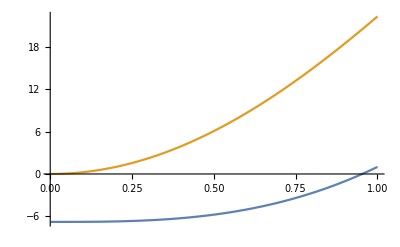

```mathematica
s=NDSolve[{D[x^2 D[y[x],x],x]==100 x^2 Sin[x],y'[0.001]==0,y[1]==1},y,{x,0.001,1}]
Plot[Evaluate[{y[x],y'[x]}/.s],{x,0.001,1}]
```

```mathematica
g[x_]=y[x]/.s[[1,1]]
g[t]
g[0.0001]
```

(2-2 ⅇ^x-x+ⅇ x+ⅇ^x x)/x/.x^2 (ⅇ^x-(2 (-1+ⅇ-ⅇ^x+ⅇ^x x))/x^2+(2 (2-2 ⅇ^x-x+ⅇ x+ⅇ^x x))/x^3)+2 x ((-1+ⅇ-ⅇ^x+ⅇ^x x)/x-(2-2 ⅇ^x-x+ⅇ x+ⅇ^x x)/x^2)==ⅇ^x x^2

(2-2 ⅇ^t-t+ⅇ t+ⅇ^t t)/t/.t^2 (ⅇ^t-(2 (-1+ⅇ-ⅇ^t+ⅇ^t t))/t^2+(2 (2-2 ⅇ^t-t+ⅇ t+ⅇ^t t))/t^3)+2 t ((-1+ⅇ-ⅇ^t+ⅇ^t t)/t-(2-2 ⅇ^t-t+ⅇ t+ⅇ^t t)/t^2)==ⅇ^t t^2

0.718282/.False

NDSolve::eerr: Warning: scaled local spatial error estimate of 10.0854 at t = 10. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

-Graphics3D-

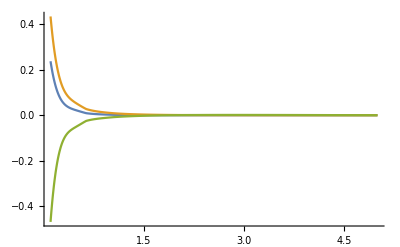

```mathematica
sol=NDSolve[{x^2 D[u[t,x],t]==D[x^2 D[u[t,x],x],x]+u[t,x]^2,u[0,x]==0,u[t,0.01]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0.01,5}];
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0.1,5},PlotRange->All]
Plot[{Evaluate[u[0.5,x]/.sol],Evaluate[u[1,x]/.sol],Evaluate[u[5,x]/.sol]},{x,0.1,5},PlotRange->All]
```

-Graphics3D-

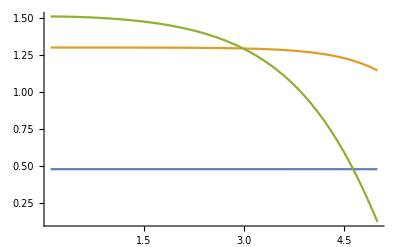

```mathematica
sol=NDSolve[{x^2 D[u[t,x],t]==D[x^2 D[u[t,x],x],x]+x^2 Cos[u[t,x]],u[0,x]==0,Derivative[0,1][u][t,0.01]==0,Derivative[0,1][u][t,5]+u[t,5]==Sin[t]},u,{t,0,10},{x,0.01,5}];
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0.1,5},PlotRange->All]
Plot[{Evaluate[u[0.5,x]/.sol],Evaluate[u[2,x]/.sol],Evaluate[u[5,x]/.sol]},{x,0.1,5},PlotRange->All]
```

-Graphics3D-

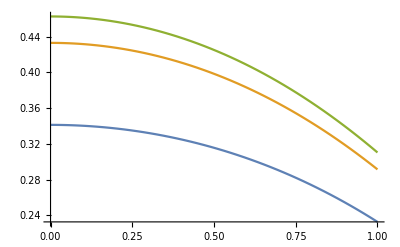

```mathematica
sol=NDSolve[{x^2 D[u[t,x],t]==D[x^2 D[u[t,x],x],x]+x^2 Cos[u[t,x]],u[0,x]==0,Derivative[0,1][u][t,0.00001]==0,Derivative[0,1][u][t,1]+u[t,1]==HeavisideTheta[t-0.000001]},u,{t,0,3},{x,0.00001,1}];
Plot3D[Evaluate[u[t,x]/.sol],{t,0,3.},{x,0.00001,1},PlotRange->All]
Plot[{Evaluate[u[0.5,x]/.sol],Evaluate[u[1,x]/.sol],Evaluate[u[3,x]/.sol]},{x,0.00001,1},PlotRange->All]
```